```mathematica
Needs["RG`FeynmanDiagrams`"]
```

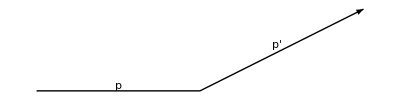

```mathematica
electronLine[{{-2,0},{0,0},{2,1}},{p,p'}]
```

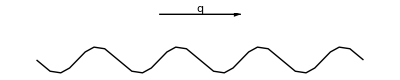

```mathematica
photonLine[{{0,0},{1,0}},q,4]
```

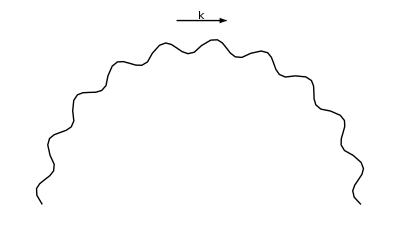

```mathematica
photonArc[{{-1,1},{1,1}},k,10]
```

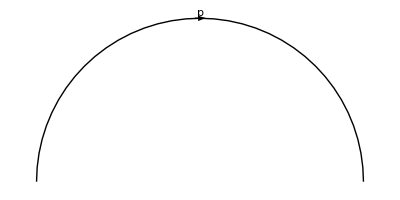

```mathematica
electronArc[{{-1,1},{1,1}},p]
```

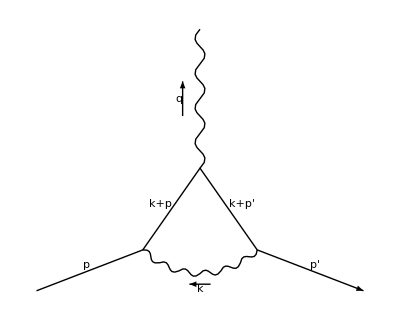

```mathematica
fig`electron vertex=With[{
pIn={-2,-1.5},pOut={2,-1.5},qOut={0,1.7},
v1={-0.7,-1},v2={0,0},v3={0.7,-1}
},
Show[{
electronLine[{pIn,v1,v2,v3,pOut},{p,p+k,p'+k,p'}],
photonArc[{v3,v1},k,6,π/2],
photonLine[{v2,qOut},q]
}]
]
```

```mathematica
Manipulate[Show[{
photonArc[{{0,0},x},k,nWiggles,arcAngle,flip]},
PlotRange->{{-1,1},{-1,1}}
],{{x,{0.5,0.5}},Locator},{{arcAngle,π},0.01,π},{flip,{True,False}},{{nWiggles,8},1,10,1}]
```

```mathematica
Manipulate[Show[{
electronArc[{{0,0},x},k,arcAngle,flip,Automatic,2]},
PlotRange->{{-1,1},{-1,1}}
],{{x,{0.5,0.5}},Locator},{{arcAngle,π},0.01,π},{flip,{True,False}}]
```